```mathematica
MyTeXForm[a_]:=StringReplace[ToString[TeXForm[a]],Shortest["\\text{"~~s___~~"}"]->s]
```

```mathematica
Clear@data
data={HS->4500,WS->4000,Nrack->5,vwind->70(*m/s*),Lrack->4300, HSup->3200,HSdown->1300,B1->300,H1->900,B2->600,H2->600,B3->600,H3->400,L1->6800,L2->7420,KD->0.613,t1->10,t2->8, ρ->7750*10^-9,g->9.81,d1->1390+2130+350,d2->800,d3->850,d4->850,d5->800,σz->-54*10^3,σy->-31*10^3,B4->60,H4->100};
data=Union[data,{B1in->B1-2 t1,H1in->H1-2 t1,B2in->B2-2 t1,H2in->H2-2 t1,B3in->B3-2 t2,H3in->H3-2 t2,Lrackdown->1200,Lrackup->Lrack-1200,d6->L2-d1-d2-d3-d4-d5}/.data]
```

{B1→300,B1in→280,B2→600,B2in→580,B3→600,B3in→584,B4→60,d1→3870,d2→800,d3→850,d4→850,d5→800,d6→250,g→9.81,H1→900,H1in→880,H2→600,H2in→580,H3→400,H3in→384,H4→100,HS→4500,HSdown→1300,HSup→3200,KD→0.613,L1→6800,L2→7420,Lrack→4300,Lrackdown→1200,Lrackup→3100,Nrack→5,t1→10,t2→8,vwind→70,WS→4000,ρ→31/4000000,σy→-31000,σz→-54000}

## Wind force

```mathematica
{d1,d2,d3,d4,d5,d6}/.data
```

{3870,800,850,850,800,250}

```mathematica
rack
```

rack

```mathematica
3870+800+850+850+800
```

7170

Area in m^2

```mathematica
Asign =(WS HS)/1000^2
```

(HS WS)/1000000

```mathematica
Asign/.data
```

18

Pressure in Pa, velocity in m/s

```mathematica
P =KD*vwind^2
```

KD vwind^2

Total force in N

```mathematica
Ftot=P*Asign
```

(HS KD vwind^2 WS)/1000000

```mathematica
Frack=Ftot/Nrack
```

(HS KD vwind^2 WS)/(1000000 Nrack)

Force per unit length on the rack 	(N/mm)

```mathematica
Fdistrack=Frack/Lrack
```

(HS KD vwind^2 WS)/(1000000 Lrack Nrack)

#### Values

```mathematica
P/.data
```

3003.7

```mathematica
Ftot/.data
```

54066.6

```mathematica
Frack/.data
```

10813.3

```mathematica
Fdistrack/.data
```

2.51473

Upper surface:

```mathematica
UpS=(HSup  WS)/1000^2/.data//N
```

12.8

Lower surface:

```mathematica
LwS=(HSdown WS)/1000^2/.data;
```

```mathematica
UpF=P*UpS/.v->vwind/.data
LwF=P*LwS/.v->vwind/.data
```

38447.4

15619.2

```mathematica
UpFRack=UpF/Nrack/.data
LwFRack=LwF/Nrack/.data
```

7689.47

3123.85

```mathematica
UpFRack=Fdistrack*Lrackup/.data
```

7795.65

```mathematica
LwFRack=Fdistrack*Lrackdown/.data
```

3017.67

### Weights

#### Vertical pillar

```mathematica
m1=(H2-H1)/L1;m2=(B2-B1)/L1;
```

```mathematica
Vtotv=Integrate[(H1+m1 x )(B1+m2 x),{x,0,L1}]//Simplify
```

1/6 (B1 (2 H1+H2)+B2 (H1+2 H2)) L1

```mathematica
m1in=(H2in-H1in)/L1;m2in=(B2in-B1in)/L1;
```

```mathematica
Vinv=Integrate[(H1in+m1in x )(B1in+m2in x),{x,0,L1}]//Simplify
```

1/6 (B1in (2 H1in+H2in)+B2in (H1in+2 H2in)) L1

```mathematica
Vv=(Vtotv-Vinv)/.data//N
```

1.6048×10^8

```mathematica
Vtotv/1000^3/.data//N
```

2.244

```mathematica
(B1+B2)/2(H1+H2)/2*L1/1000^3/.data//N
```

2.295

```mathematica
mvert=ρ Vv/.data
```

1243.72

```mathematica
wvert=(mvert g)/L1/.data
```

1.79425

#### Horizontal pillar

```mathematica
Vtoth=B3 H3 L2
```

B3 H3 L2

```mathematica
Vinh=B3in H3in L2
```

B3in H3in L2

```mathematica
Vh=(Vtoth-Vinh)/.data//N
```

1.1682×10^8

```mathematica
mhor=ρ Vh/.data
```

905.359

```mathematica
whor=(mhor g)/L2/.data
```

1.19698

#### Rackets

```mathematica
Prack=ρ B4 H4 Lrack g/.data
```

1961.51

## Nut loads

```mathematica
data=Union[data,{Anut->459,Anutint->π*27*22,σy->440}]//N(*mm^2, MPa*)
```

{Anut→459.,Anutint→1866.11,B1→300.,B1in→280.,B2→600.,B2in→580.,B3→600.,B3in→584.,B4→60.,d1→3870.,d2→800.,d3→850.,d4→850.,d5→800.,d6→250.,g→9.81,H1→900.,H1in→880.,H2→600.,H2in→580.,H3→400.,H3in→384.,H4→100.,HS→4500.,HSdown→1300.,HSup→3200.,KD→0.613,L1→6800.,L2→7420.,Lrack→4300.,Lrackdown→1200.,Lrackup→3100.,Nrack→5.,t1→10.,t2→8.,vwind→70.,WS→4000.,ρ→7.75×10^-6,σy→-31000.,σy→440.,σz→-54000.}

```mathematica
loads={Mx->425*10^6,T->299*10^6,Vz->Vz}
```

{Mx→425000000,T→299000000,Vz→Vz}

```mathematica
norm[x_,y_]:=Norm[{x,y}]
```

```mathematica
Htot=880;
Btot=500;
nb=20;
A;
rimax=√((170*3)^2+(105*2)^2)
himax=170*7
```

390 √2

1190

```mathematica
radius={norm[105*2,0],norm[105*2,170],norm[105*2,2*170],norm[105*2,3*170],norm[105,3*170],norm[0,3*170],norm[-105,3*170],norm[-105*2,3*170],norm[-105*2,2*170],norm[-105*2,170],norm[-105*2,0],norm[-105*2,-170],norm[-105*2,-2*170],norm[-105*2,-3*170],norm[-105,-3*170],norm[0,-3*170],norm[105,-3*170],norm[105*2,-3*170],norm[105*2,2*170],norm[105*2,170]}
```

{210,10 √730,10 √1597,390 √2,15 √1205,510,15 √1205,390 √2,10 √1597,10 √730,210,10 √730,10 √1597,390 √2,15 √1205,510,15 √1205,390 √2,10 √1597,10 √730}

### Shear

#### Shear

```mathematica
Vishear=Vz/nb;
```

#### Shear due to torsion

```mathematica
Vitorsionloc=T*(Max@radius)/(∑_(i=1)^nb radius[[i]]^2)
```

(39 T)/(192025 √2)

#### Total shear

The most stressed joint due to shear is the one at {2*150, -3*170}

```mathematica
α=ArcTan[2*105,-3*170]//N//Abs
α*180/π
```

1.18019

67.6199

```mathematica
Vitorsion=Vitorsionloc*{Cos[π/2-α],Sin[π/2-α]}
```

{0.000132795 T,0.0000546804 T}

```mathematica
Vi=√(Vitorsion[[1]]^2+(Vishear-Vitorsion[[2]])^2)/.loads/.Vz->1
```

42940.1

### Normal force

```mathematica
heigths={0,0,0,0,0,170,170*2,170*3,170*4,170*5,170*6,170*6,170*6,170*6,170*6,170*5,170*4,170*3,170*2,170*1};
```

```mathematica
Ni=Mx himax/(∑_(i=1)^nb heigths[[i]]^2)/.loads//N
```

60344.8

```mathematica
100000/6/.data//N
```

16666.7

```mathematica
17000*6
```

102000

### Max Preload

```mathematica
N0=0.8 Anut σy /.data
```

-1.13832×10^7

## Constraint reactions and internal actions

### Constraint reactions

```mathematica
Mrack=UpFRack Lrackup-LwFRack Lrackdown/.data
```

2.05453×10^7

```mathematica
Rxa=5 Frack
Rya=0
Rza=wvert L1+whor L2+5 Prack
Mxa=whor L2^2/2+Prack ((d1)+(d1+d2)+(d1+d2+d3)+(d1+d2+d3+d4)+(d1+d2+d3+d4+d5))
Mya=5 Mrack+5 Frack L1
Mza=Frack((d1)+(d1+d2)+(d1+d2+d3)+(d1+d2+d3+d4)+(d1+d2+d3+d4+d5))
```

(HS KD vwind^2 WS)/(200000 Nrack)

0

9807.55+1.79425 L1+1.19698 L2

1961.51 (5 d1+4 d2+3 d3+2 d4+d5)+0.598488 L2^2

1.02727×10^8+(HS KD L1 vwind^2 WS)/(200000 Nrack)

((5 d1+4 d2+3 d3+2 d4+d5) HS KD vwind^2 WS)/(1000000 Nrack)

```mathematica
{Rxa,Rya,Rza,Mxa,Mya,Mza}/.data
```

{54066.6,0,30890.,8.70883×10^7,4.70085×10^8,2.98448×10^8}

### Vertical pillar

```mathematica
plotaction1[ac_,acname_]:=Plot[ac,{z1,0,L1/.data},Filling->Axis,Exclusions->None,AxesOrigin->{0,0},AxesStyle->{Black,Bold},TicksStyle->Medium,LabelStyle->Directive[Black,Bold],GridLines->{{L1}/.data,{}},GridLinesStyle->Directive[Thickness@0.005,Dashed],PlotRange->All,AxesLabel->{Style["z_1 [ mm ]",Bold,Black,16]},PlotLabel->Style[ToString@acname,Bold,Black,16]]
```

```mathematica
Nv=wvert z1-Rza/.data
Tyv=Rya/.data
Tzv=-Rxa/.data
Mxv=Mza/.data
Myv=Mya-Rxa z1/.data
Mzv=-Mxa-Rya z1/.data
```

-30890.+1.79425 z1

0

-54066.6

2.98448×10^8

4.70379×10^8-54066.6 z1

-8.70883×10^7

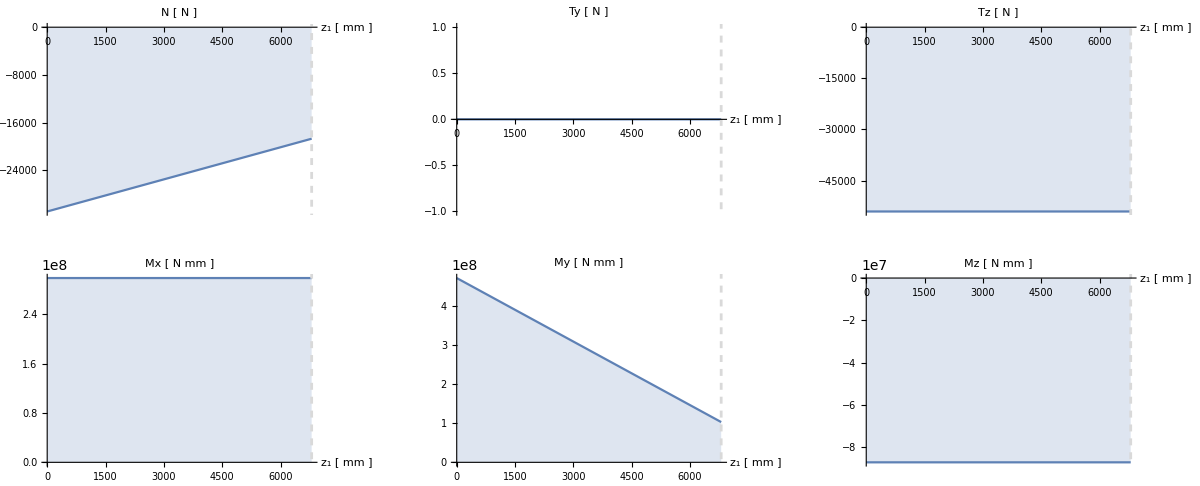

```mathematica
GraphicsGrid[{
{plotaction1[Nv,"N [ N ]"],plotaction1[Tyv,"Ty [ N ]"],plotaction1[Tzv,"Tz [ N ]"]},
{plotaction1[Mxv,"Mx  [ N mm ]"],plotaction1[Myv,"My [ N mm ]"],plotaction1[Mzv,"Mz [ N mm ]"]}},ImageSize->1200]
```

### Horizontal pillar

```mathematica
d={d1,d2,d3,d4,d5}
Nh=-Rya/.data
Tyh=Piecewise[{{-Rza+wvert L1+whor z2, 0<=z2<d1}, {-Rza+wvert L1+whor z2+Prack, d1<=z2<d1+d2}, {-Rza+wvert L1+whor z2+2Prack, d1+d2<=z2<d1+d2+d3}, {-Rza+wvert L1+whor z2+3Prack, d1+d2+d3<=z2<d1+d2+d3+d4}, {-Rza+wvert L1+whor z2+4Prack, d1+d2+d3+d4<=z2<d1+d2+d3+d4+d5}, {-Rza+wvert L1+whor z2+5Prack, d1+d2+d3+d4+d5<=z2<=L2}}]/.data;
Tzh=Piecewise[{{-Rxa, 0<=z2<d1}, {-Rxa+Frack, d1<=z2<d1+d2}, {-Rxa+2Frack, d1+d2<=z2<d1+d2+d3}, {-Rxa+3Frack, d1+d2+d3<=z2<d1+d2+d3+d4}, {-Rxa+4Frack, d1+d2+d3+d4<=z2<d1+d2+d3+d4+d5}, {-Rxa+5Frack, d1+d2+d2+d3+d4+d5<=z2<=L2}}]/.data;
Mxh=Piecewise[{{-Mya+Rxa L1, 0<=z2<d1}, {-Mya+Rxa L1+Mrack, d1<=z2<d1+d2}, {-Mya+Rxa L1+2Mrack, d1+d2<=z2<d1+d2+d3}, {-Mya+Rxa L1+3Mrack, d1+d2+d3<=z2<d1+d2+d3+d4}, {-Mya+Rxa L1+4Mrack, d1+d2+d3+d4<=z2<d1+d2+d3+d4+d5}, {-Mya+Rxa L1+5Mrack, d1+d2+d3+d4+d5<=z2<=L2}}]/.data;

Myhtmp=-Mza+Rxa z2/.data;

Myh=Piecewise[{{Myhtmp, 0<=z2<d1}, {Myhtmp-Frack(z2-d1), d1<=z2<d1+d2}, {Myhtmp-Frack(z2-d1)-Frack(z2-∑_(i=1)^2 d[[i]]), d1+d2<=z2<d1+d2+d3}, {Myhtmp-Frack(z2-d1)-Frack(z2-∑_(i=1)^2 d[[i]])-Frack(z2-∑_(i=1)^3 d[[i]]), d1+d2+d3<=z2<d1+d2+d3+d4}, {Myhtmp-Frack(z2-d1)-Frack(z2-∑_(i=1)^2 d[[i]])-Frack(z2-∑_(i=1)^3 d[[i]])-Frack(z2-∑_(i=1)^4 d[[i]]), d1+d2+d3+d4<=z2<d1+d2+d3+d4+d5}, {Myhtmp-Frack(z2-d1)-Frack(z2-∑_(i=1)^2 d[[i]])-Frack(z2-∑_(i=1)^3 d[[i]])-Frack(z2-∑_(i=1)^4 d[[i]])-Frack(z2-∑_(i=1)^5 d[[i]]), d1+d2+d3+d4+d5<=z2<=L2}}]/.data;
Mzhtmp=-Mxa-Rya L1+Rza z2-wvert L1 z2-whor z2^2/2/.data
Mzh=Piecewise[{{Mzhtmp, 0<=z2<d1}, {Mzhtmp-Prack(z2-d1), d1<=z2<d1+d2}, {Mzhtmp-Prack(z2-d1)-Prack(z2-∑_(i=1)^2 d[[i]]), d1+d2<=z2<d1+d2+d3}, {Mzhtmp-Prack(z2-d1)-Prack(z2-∑_(i=1)^2 d[[i]])-Prack(z2-∑_(i=1)^3 d[[i]]), d1+d2+d3<=z2<d1+d2+d3+d4}, {Mzhtmp-Prack(z2-d1)-Prack(z2-∑_(i=1)^2 d[[i]])-Prack(z2-∑_(i=1)^3 d[[i]])-Prack(z2-∑_(i=1)^4 d[[i]]), d1+d2+d3+d4<=z2<d1+d2+d3+d4+d5}, {Mzhtmp-Prack(z2-d1)-Prack(z2-∑_(i=1)^2 d[[i]])-Prack(z2-∑_(i=1)^3 d[[i]])-Prack(z2-∑_(i=1)^4 d[[i]])-Prack(z2-∑_(i=1)^5 d[[i]]), d1+d2+d3+d4+d5<=z2<=L2}}]/.data;
```

{d1,d2,d3,d4,d5}

0

-8.70883×10^7+18689.1 z2-0.598488 z2^2

```mathematica
plotaction2[ac_,acname_]:=Plot[ac,{z2,0,L2/.data},Filling->Axis,Exclusions->None,AxesOrigin->{0,0},AxesStyle->{Black,Bold},TicksStyle->Medium,LabelStyle->Directive[Black,Bold],GridLines->{{d1,d1+d2,d1+d2+d3,d1+d2+d3+d4,d1+d2+d3+d4+d5,L2}/.data,{}},GridLinesStyle->Directive[Thickness@0.005,Dashed],PlotRange->All,AxesLabel->{Style["z_2 [ mm ]",Bold,Black,16]},PlotLabel->Style[ToString@acname,Bold,Black,16]]
```

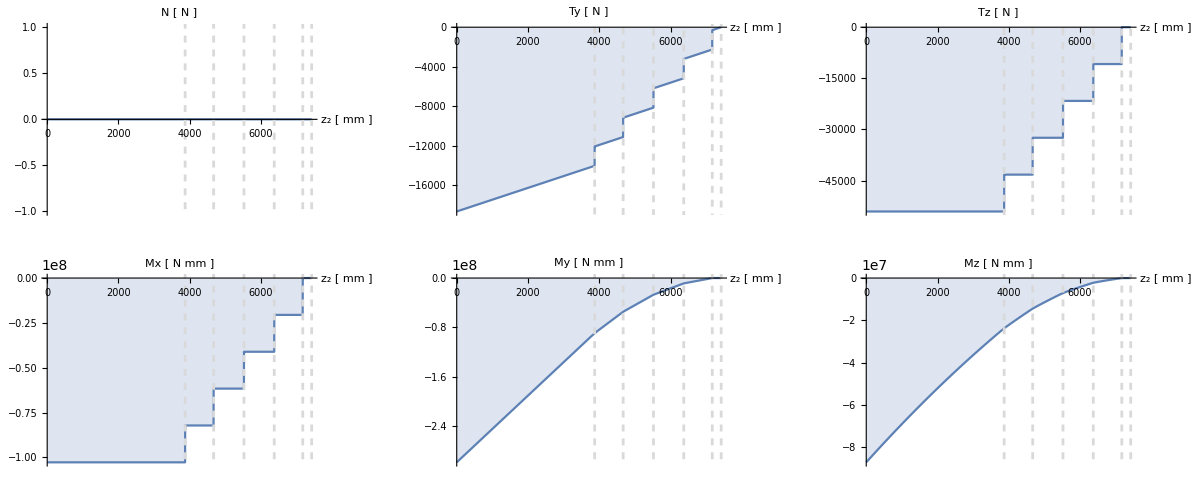

```mathematica
GraphicsGrid[{
{plotaction2[Nh,"N [ N ]"],plotaction2[Tyh,"Ty [ N ]"],plotaction2[Tzh,"Tz [ N ]"]},
{plotaction2[Mxh,"Mx  [ N mm ]"],plotaction2[Myh,"My [ N mm ]"],plotaction2[Mzh,"Mz [ N mm ]"]}},ImageSize->1200]
```

```mathematica
{Nh,Tyh,Tzh,Mxh,Myh,Mzh}/.z2->0/.data
```

{0,-18689.1,-54066.6,-1.02727×10^8,-2.98448×10^8,-8.70883×10^7}

### Stresses

#### Vertical pillar

```mathematica
{Nv,Tyv,Tzv,Mxv,Myv,Mzv}/.z1->0/.data
```

{-30890.,0,-54066.6,2.98448×10^8,4.70379×10^8,-8.70883×10^7}

```mathematica
Av=B1 H1-(B1-2t1)(H1-2t1)/.data
```

23600.

```mathematica
{B1,H1}/.data
```

{300.,900.}

```mathematica
Iy=(B1 H1^3)/12-((B1-2t1)(H1-2t1)^3)/12/.data//N
```

2.32399×10^9

```mathematica
Iz=(B1^3 H1)/12-((B1-2t1)^3(H1-2t1))/12/.data//N
```

4.15187×10^8

```mathematica
{Myv,Mzv}/.data/.z1->0
```

{4.70379×10^8,-8.70883×10^7}

```mathematica
{B1,H1}/.data
```

{300.,900.}

```mathematica
σxbmy=My/Iy z/.My->Myv/.z->H1/2/.z1->0/.data
```

91.0809

```mathematica
σxbmz=-Mz/Iz y/.Mz->Mzv/.y->B1/2/.z1->0/.data
```

31.4635

```mathematica
σxa=Nv/A/.A->Av/.z1->0
```

-1.3089

```mathematica
Tzv
```

-54066.6

```mathematica
σxv=σxbmy+σxbmz+σxa
```

121.236

```mathematica
τyxv=(Tzv H1 y)/(4Iy)/.y->(B1/2)/.data
```

-0.78518

```mathematica
τzxv=Tzv/(4Iy)((B1 H1)/2+(H1^2/4-z^2))/.z->(H1/2)/.data
```

-0.78518

```mathematica
τtors=Mxv/(2 t1(B1-t1)(H1-t1))/.data
```

57.8163

```mathematica
σeq=√(1/2((σx-σy)^2+(σy-σz)^2+(σz-σx)^2+6(τyx^2+τxz^2+τyz^2)))
```

(√((σx-σy)^2+(σy-σz)^2+(-σx+σz)^2+6 (τxz^2+τyx^2+τyz^2)))/(√2)

```mathematica
σeq/.σx->σxv/.σy->0/.σz->0/.τxy->τy/.τxz->0/.τyz->τtors
```

157.246

```mathematica
MyTeXForm@σeq
```

\frac{\sqrt{($\sigma $x-$\sigma $y)^2+($\sigma $z-$\sigma $x)^2+($\sigma $y-$\sigma $z)^2+6 \left($\tau $xy^2+$\tau $xz^2+$\tau $yz^2\right)}}{\sqrt{2}}

#### Area vertical pillar

```mathematica
Av=23954;
```

```mathematica
Ftz=σz Av /.data
```

-1.29352×10^9

```mathematica
Tyh/.z2->d1-10/.data
```

-14068.8

```mathematica
Tyh/.z2->d1+10/.data
```

-12083.3